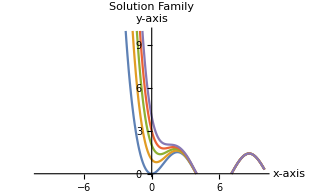
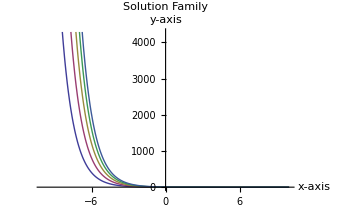
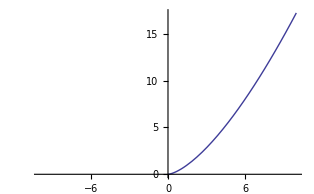
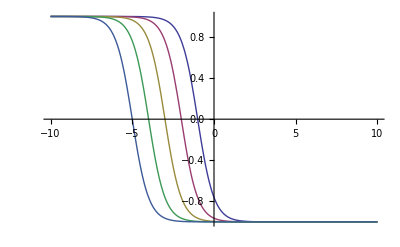
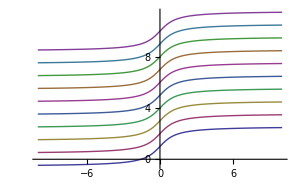
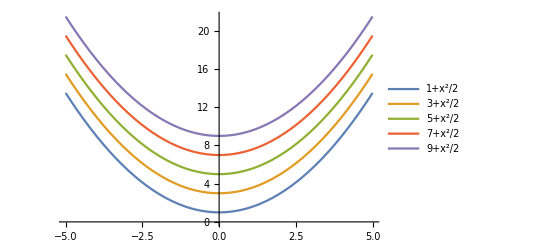
```mathematica
Plot the Solution Family
Question1
sol=DSolve[y'[x]+y[x]==2 Sin[N[x]],y[x],x]
{{y[x]->ⅇ^-x C[1]-Cos[x]+Sin[x]}}
y[x]/.sol[[1]]
ⅇ^-x C[1]-Cos[x]+Sin[x]
table=Table[y[x]/.sol/.{C[1]->k},{k,1,5,1}]
{{ⅇ^-x-Cos[x]+Sin[x]},{2 ⅇ^-x-Cos[x]+Sin[x]},{3 ⅇ^-x-Cos[x]+Sin[x]},{4 ⅇ^-x-Cos[x]+Sin[x]},{5 ⅇ^-x-Cos[x]+Sin[x]}}
Plot[table,{x,-10,10},PlotRange->{0,10},AxesLabel->{"x-axis","y-axis"},PlotLabel->"Solution Family"]
-Graphics-
-Graphics-
Question2 dy/dx=y^(1/3) with y(0)=0
sol3=DSolve[{y'[x]==y[x]^(1/3),y[0]==0},y[x],x]
{{y[x]->2/3 √(2/3) x^(3/2)}}
Plot[y[x]/.sol3,{x,-10,10}]
-Graphics-
Question3:dy/dx=y^2-1
sol2=DSolve[y'[x]==y[x]^2-1,y[x],x]
{{y[x]->(1-ⅇ^(2 x+2 C[1]))/(1+ⅇ^(2 x+2 C[1]))}}
table2=Table[y[x]/.sol2/.{C[1]->k},{k,1,5,1}]
{{(1-ⅇ^(2+2 x))/(1+ⅇ^(2+2 x))},{(1-ⅇ^(4+2 x))/(1+ⅇ^(4+2 x))},{(1-ⅇ^(6+2 x))/(1+ⅇ^(6+2 x))},{(1-ⅇ^(8+2 x))/(1+ⅇ^(8+2 x))},{(1-ⅇ^(10+2 x))/(1+ⅇ^(10+2 x))}}
Plot[table2,{x,-10,10}]
-Graphics-
Question4:dy/dt=1/(1+t^2)
sol4=DSolve[y'[t]==1/(1+t^2),y[t],t]
{{y[t]->ArcTan[t]+C[1]}}
table4=Table[y[t] /.sol4 /.{C[1]->k},{k,1,10,1}]
{{1+ArcTan[t]},{2+ArcTan[t]},{3+ArcTan[t]},{4+ArcTan[t]},{5+ArcTan[t]},{6+ArcTan[t]},{7+ArcTan[t]},{8+ArcTan[t]},{9+ArcTan[t]},{10+ArcTan[t]}}
Plot[table4,{t,-10,10}]
-Graphics-
Question5:y’[x]==x
s1 = DSolve[y'[x]==x,y[x],x]
{{y[x]->x^2/2+C[1]}}
y[x]/.s1[[1]]
x^2/2+C[1]
[x]/.s1[[1]]
a=Table[%/.{C[1]->k},{k,1,10,2}]
{1+x^2/2,3+x^2/2,5+x^2/2,7+x^2/2,9+x^2/2}
Plot[a,{x,-5,5}, PlotLegends->"Expressions"]
-Graphics-
```

# Q2 Solve the following differential equation

```mathematica
s1 = DSolve[y'[x]==x,y[x],x]
```

{{y[x]→x^2/2+C[1]}}

```mathematica
y[x]/.s1[[1]]
```

x^2/2+C[1]

```mathematica
[x]/.s1[[1]]
```

x^2/2+C[1]

```mathematica
a=Table[%/.{C[1]->k},{k,1,10,2}]
```

{1+x^2/2,3+x^2/2,5+x^2/2,7+x^2/2,9+x^2/2}

Set::write: Tag Integer in 5[1] is Protected.

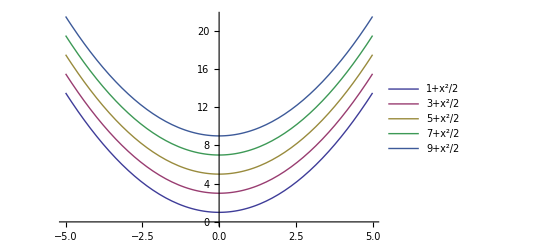

```mathematica
Plot[a,{x,-5,5}, PlotLegends->"Expressions"]
```